```mathematica
jln[l_,n_,k_,p_]:=NIntegrate[x^n SphericalBesselJ[l,k x]Exp[-p x^2],{x,1,Infinity},WorkingPrecision->128,AccuracyGoal->64]
```

```mathematica
j0n[n_,k_,p_]:=NIntegrate[x^(n-1) Sin[k x]Exp[-p x^2],{x,1,Infinity},WorkingPrecision->32,AccuracyGoal->16]/k
```

```mathematica
j0nZero[n_,k_,p_]:=NIntegrate[x^(n-1) Sin[k x]Exp[-p x^2],{x,0,1},WorkingPrecision->32,AccuracyGoal->16]/k
```

```mathematica
j0nFull[n_,k_,p_]:=NIntegrate[x^(n-1) Sin[k x]Exp[-p x^2],{x,0,Infinity},WorkingPrecision->32,AccuracyGoal->16]/k
```

```mathematica
j20n[n_,k_,p_]:=NIntegrate[x^(n-1) Cos[k x]Exp[-p x^2],{x,1,Infinity},WorkingPrecision->32,AccuracyGoal->16]/k
```

```mathematica
Rationalize[63.11246667875]
```

63.1125

```mathematica
jln[0,4,120,SetPrecision[1.605285815000000,128]]
```

0.0000113742421761714526040497992239898803787970401144580509580682619495453409742408272475089884116278912626066528141755926885768159

```mathematica
jln[2,6,120,SetPrecision[1.605285815000000,128]]
```

-0.000011031418758002934361399256470341854546018977780642330396361686476992274571047390251313673703458052937204364356474508431807160031

```mathematica
jln[7,12,120,SetPrecision[1.605285815000000,256]]
```

-0.000011098120769005470984602255251111152373417661339237802228281813409362627663740135980552707353678606646899541514314531585333664213

```mathematica
ll=1;nn=6;kk=5;pp=2;
```

```mathematica
jln[ll,nn,kk,pp]
```

-0.0081025797110355416429787888866429158798489661326412256109992510049745239067475046114538536801965131403670353007146495285725873052

```mathematica
1/kk Exp[-pp]SphericalBesselJ[0,kk]+nn/kk jln[ll-1,nn-1,kk,pp]-2pp/kk jln[ll-1,nn+1,kk,pp]
```

-0.0081025797110355416429787888866429158798489661326412256109992510049745239067475046058972052539256347185713494319517712253546533955

```mathematica
j0n[nn+1,kk,pp]
```

0.0034503697708702942865005526204535

```mathematica
1/kk^2Cos[kk]Exp[-pp]+nn j20n[nn,kk,pp]/kk-2pp j20n[nn+2,kk,pp]/kk
```

0.003450369770870294285802919892584

```mathematica
j20n[nn+1,kk,pp]
```

0.009086181031142579411016238144681

```mathematica
-1/kk^2Sin[kk]Exp[-pp]-nn j0n[nn,kk,pp]/kk+2pp j0n[nn+2,kk,pp]/kk
```

0.009086181031142579411358906279596

```mathematica
Exp[-pp](Cos[kk]+(2pp-nn)/kk Sin[kk])-nn(nn-1)j0n[nn-1,kk,pp]+(2pp(2nn+1)-kk^2)j0n[nn+1,kk,pp]-4pp^2j0n[nn+3,kk,pp]
```

1.668890451779×10^-19

```mathematica
Integrate[Sin[k x]Exp[-p x^2],{x,1,Infinity}]/k
```

ConditionalExpression[(ⅇ^(-k^2/(4 p)) √π (Erfi[(k-2 ⅈ p)/(2 √p)]+Erfi[(k+2 ⅈ p)/(2 √p)]))/(4 k √p),Re[p]>0]

```mathematica
Integrate[x Sin[k x]Exp[-p x^2],{x,1,Infinity}]/k
```

ConditionalExpression[(ⅇ^(-k^2/(4 p)) (2 ⅈ ⅇ^((k-2 ⅈ p)^2/(4 p)) √p-2 ⅈ ⅇ^((k+2 ⅈ p)^2/(4 p)) √p+2 k √π-ⅈ k √π Erfi[(k-2 ⅈ p)/(2 √p)]+ⅈ k √π Erfi[(k+2 ⅈ p)/(2 √p)]))/(8 k p^(3/2)),Re[p]>0]

```mathematica
ll=0;nn=1;kk=200;pp=1;
```

```mathematica
j0n[nn,kk,pp]
```

4.40011310567730211701955162495×10^-6

```mathematica
j0nFull[nn,kk,pp]-j0nZero[nn,kk,pp]
```

4.40011310567730143335257751012×10^-6

```mathematica
j0nZero[nn,kk,pp]
```

0.00002060113708186958927952561692144

```mathematica
j0nFull[nn,kk,pp]
```

0.000025001250187546890712878194431563

```mathematica
Integrate[x^(2n+1)Exp[-p x^2],{x,1,Infinity}]
```

ConditionalExpression[1/2 ExpIntegralE[-n,p],Re[p]>0&&Re[n]>-1]

```mathematica
Integrate[x Exp[-p x^2],{x,1,Infinity}]
```

ConditionalExpression[ⅇ^-p/(2 p),Re[p]>0]

```mathematica
Integrate[Sin[k x]Exp[-p x^2],{x,1,Infinity},Assumptions->{k>0,p>0}]/k
```

(ⅇ^(-k^2/(4 p)) √π (Erfi[(k-2 ⅈ p)/(2 √p)]+Erfi[(k+2 ⅈ p)/(2 √p)]))/(4 k √p)

```mathematica
lux=CoefficientList[Integrate[Normal[Series[Sin[k x],{x,0,100}]]Exp[-p x^2],{x,1,Infinity},Assumptions->{k>0,p>0}]/k,k];
```

$Aborted

```mathematica
j0n[1,5,1]
```

-0.002193991691828569232456011974313

```mathematica
Table[Re[lux[[n]]]k^n,{n,1,99}]/.{p->20,k->10}//N
```

{5.15288×10^-10,0.,-9.01755×10^-9,0.,4.74495×10^-8,0.,-1.19186×10^-7,0.,1.75107×10^-7,0.,-1.68888×10^-7,0.,1.15229×10^-7,0.,-5.86097×10^-8,0.,2.31062×10^-8,0.,-7.27629×10^-9,0.,1.8748×10^-9,0.,-4.03104×10^-10,0.,7.35308×10^-11,0.,-1.15407×10^-11,0.,1.57767×10^-12,0.,-1.89897×10^-13,0.,2.03204×10^-14,0.,-1.95013×10^-15,0.,1.69204×10^-16,0.,-1.33726×10^-17,0.,9.69437×10^-19,0.,-6.48917×10^-20,0.,4.03586×10^-21,0.,-2.34598×10^-22,0.,1.28164×10^-23,0.,-6.61475×10^-25,0.,3.2407×10^-26,0.,-1.51363×10^-27,0.,6.76588×10^-29,0.,-2.08178×10^-30,0.,1.46853×10^-30,0.,-9.45049×10^-33,0.,7.29426×10^-36,0.,-8.99188×10^-36,0.,3.65688×10^-37,0.,-4.21779×10^-39,0.,3.53222×10^-40,0.,-9.22723×10^-42,0.,2.94652×10^-43,0.,-1.04454×10^-44,0.,3.17394×10^-46,0.,-9.54086×10^-48,0.,2.84781×10^-49,0.,-8.15292×10^-51,0.,2.28903×10^-52,0.,-6.27957×10^-54,0.,1.69045×10^-55,0.,-4.44729×10^-57,0.,1.14628×10^-58,0.,-2.89445×10^-60}

```mathematica
Integrate[Exp[-x t^2],{t,0,1}]
```

(√π Erf[√x])/(2 √x)

```mathematica
Integrate[Exp[-p x^2]Exp[I k x],{x,1,Infinity},Assumptions->{p>0}]
```

(ⅇ^(-k^2/(4 p)) √π (1+ⅈ Erfi[(k+2 ⅈ p)/(2 √p)]))/(2 √p)

```mathematica
Integrate[Exp[-p x^2]Exp[-I k x],{x,1,Infinity},Assumptions->{p>0}]
```

(ⅇ^(-k^2/(4 p)) √π Erfc[(ⅈ k+2 p)/(2 √p)])/(2 √p)

```mathematica
Integrate[Exp[-p x^2]Exp[I k x],{x,0,Infinity}]
```

ConditionalExpression[(ⅇ^(-k^2/(4 p)) √π (1+ⅈ Erfi[k/(2 √p)]))/(2 √p),Re[p]>0||(Re[p]≥0&&Im[k]>0)]

```mathematica
Integrate[Exp[-p x^2]Exp[-I k x],{x,0,Infinity}]
```

ConditionalExpression[(ⅇ^(-k^2/(4 p)) √π (1-ⅈ Erfi[k/(2 √p)]))/(2 √p),(Im[k]<0&&Re[p]≥0)||Re[p]>0]

```mathematica
Integrate[Exp[-x^2],{x,0,Infinity}]
```

(√π)/2

```mathematica
(ⅇ^(-k^2/(4 p)) √π (1+ⅈ Erfi[(k+2 ⅈ p)/(2 √p)]))/(2 √p)/.{k->kk,p->pp}//N
```

0.00161522203578863+0.0008800226211355 ⅈ

```mathematica
(ⅇ^(-k^2/(4 p)) √π (1+ⅈ Erfi[(k-2 ⅈ p)/(2 √p)]))/(2 √p)/.{k->kk,p->pp}//N
```

-0.00161522203578863+0.0008800226211355 ⅈ

```mathematica
kk=10;pp=2/10;
```

```mathematica
Erf[(k+2 ⅈ p)/(2 √p)]-Erf[(k-2 ⅈ p)/(2 √p)]/.{k->kk,p->pp}//N
```

0.+1.25127×10^8 ⅈ

```mathematica
Erf[(k+2 ⅈ p)/(2 √p)]/.{k->kk,p->pp}//N
```

6.11023×10^6+6.25636×10^7 ⅈ

```mathematica
Erf[(k-2 ⅈ p)/(2 √p)]/.{k->kk,p->pp}//N
```

6.11023×10^6-6.25636×10^7 ⅈ

```mathematica
Re[Sqrt[Pi]/(4I k)(Erf[(k+2 ⅈ p)/(2 √p)]-Erf[(k-2 ⅈ p)/(2 √p)])Exp[-k^2/(4p)]/.{k->kk,p->pp}//N]
```

-8.37086×10^-112

```mathematica
-Sqrt[Pi]/(2k)Exp[-k^2/(4p)]Im[Erf[(k-2 ⅈ p)/(2 √p)]]/.{k->kk,p->pp}//N
```

-8.37086×10^-112

```mathematica
FFOral[t_]:=1/2NIntegrate[Exp[-x^2]/(x^2+t^2),{x,-Infinity,+Infinity},WorkingPrecision->64,AccuracyGoal->32]
```

```mathematica
FFOral[2/10+3I]
```

-0.1035405577781677317920314827605385124656372245168039112212443877-0.01508486172896060777061169206791962460343272351734425907479419129 ⅈ

```mathematica
hhh=1/20; nnn=200;
```

```mathematica
FFAnal[t_]:=hhh(1/(2t^2)+Sum[Exp[-n^2hhh^2]/((n hhh)^2+t^2),{n,1,nnn}])
```

```mathematica
SetPrecision[FFAnal[2/10+3I],32]
```

-0.1035405577781661745348103558418-0.01508486172896109671059698037203 ⅈ

```mathematica
Faddeeva[z_]:=Exp[-z^2]Erfc[-I z]
```

```mathematica
DFaddeeva[z_]:=(2 ⅈ)/(√π)-2 ⅇ^(-z^2) z Erfc[-ⅈ z]
```

```mathematica
Faddeeva[I Sqrt[pp]+kk/(2Sqrt[pp])]//N
```

0.22598+0.0389922 ⅈ

```mathematica
DFaddeeva[I Sqrt[pp]+kk/(2Sqrt[pp])]//N
```

-0.0277442+0.0828896 ⅈ

```mathematica
kk=2;pp=5;
```

```mathematica
j0n[n_,k_,p_]:=NIntegrate[x^(n-1) Sin[k x]Exp[-p x^2],{x,1,Infinity},WorkingPrecision->32,AccuracyGoal->16]/k
```

```mathematica
j0n[1,kk,pp]
```

0.000252701991815998489105795537091

```mathematica
j0n[2,kk,pp]
```

0.0002717582683242875076067304073873

```mathematica
j0n[3,kk,pp]
```

NIntegrate::deoncon: DoubleExponentialOscillatory has failed to converge for the integrand ⅇ^-5\ (1 + x)^2\ (1 + x)^2\ Cos[2\ x]\ Sin[2] over {0, ∞}. DoubleExponentialOscillatory obtained 0.00064560396708916195842858251752608 and 1.8231465643253139072144465314849×10^-16 for the integral and error estimates.

0.000293462259641854579500978073446

```mathematica
MatrixForm[Table[j0n[n,kk,pp],{n,1,11}]]
```

NIntegrate::deoncon: DoubleExponentialOscillatory has failed to converge for the integrand ⅇ^-5\ (1 + x)^2\ (1 + x)^2\ Cos[2\ x]\ Sin[2] over {0, ∞}. DoubleExponentialOscillatory obtained 0.00064560396708916195842858251752608 and 1.8231465643253139072144465314849×10^-16 for the integral and error estimates.

NIntegrate::deoncon: DoubleExponentialOscillatory has failed to converge for the integrand ⅇ^-5\ (1 + x)^2\ (1 + x)^3\ Cos[2\ x]\ Sin[2] over {0, ∞}. DoubleExponentialOscillatory obtained 0.00070578504085295558755741472420081 and 1.0413732621410467406140276043079×10^-16 for the integral and error estimates.

(0.000252701991815998489105795537091
0.0002717582683242875076067304073873
0.000293462259641854579500978073446
0.00031832330055542822144535869783941
0.000346970761048265418531044014442
0.000380186054374676461582964811095
0.000418943566110255595470725119982
0.0004644627509500600952196957832211
0.0005182738690666499244474558325493
0.0005822996882901499324040994579522
0.0006589544510275408462461597659645)

```mathematica
MatrixForm[Table[jln[1,n,kk,pp],{n,1,11}]]
```

(0.00029084769758546427452645284054838
0.00031709016069578536535079551139905
0.00034772036679834989626244675675395
0.00038377018113144185112155010154515
0.00042657744660424802222779280736619
0.00047789391968257803720456192319688
0.00054003690265012689969935405990219
0.00061610438619683253657635546272066
0.00071028340491358055787029660962922
0.00082829655728460515912357738012053
0.00097805537472238683096226585382908)

```mathematica
jln[5,9,kk,pp]
```

0.00001045851605868329479066801275962

```mathematica
Table[(l+1)(l+2)/2,{l,0,20}]
```

{1,3,6,10,15,21,28,36,45,55,66,78,91,105,120,136,153,171,190,210,231}

```mathematica
SetPrecision[Im[1/(2kk)Sqrt[Pi/pp]Exp[I kk-pp]Faddeeva[I Sqrt[pp]+kk/(2Sqrt[pp])]],32]
```

0.000252701991815998491187571264

```mathematica
Faddeeva[I Sqrt[pp]+kk/(2Sqrt[pp])]//N
```

0.32579+0.061096 ⅈ

```mathematica
Integrate[x^1 Sin[k x]Exp[-p x^2],{x,1,Infinity}]
```

ConditionalExpression[(ⅇ^(-k^2/(4 p)) (2 ⅈ ⅇ^((k-2 ⅈ p)^2/(4 p)) √p-2 ⅈ ⅇ^((k+2 ⅈ p)^2/(4 p)) √p+2 k √π-ⅈ k √π Erfi[(k-2 ⅈ p)/(2 √p)]+ⅈ k √π Erfi[(k+2 ⅈ p)/(2 √p)]))/(8 p^(3/2)),Re[p]>0]

```mathematica
FullSimplify[%,Assumptions->{p>0,k>0}]
```

-(ⅈ ⅇ^(-k^2/(4 p)) k √π (2 ⅈ+Erfi[(k-2 ⅈ p)/(2 √p)]-Erfi[(k+2 ⅈ p)/(2 √p)]))/(8 p^(3/2))+(ⅇ^-p Sin[k])/(2 p)

```mathematica
Integrate[x^0 Sin[k x]Exp[-p x^2],{x,1,Infinity}]
```

ConditionalExpression[(ⅇ^(-k^2/(4 p)) √π (Erfi[(k-2 ⅈ p)/(2 √p)]+Erfi[(k+2 ⅈ p)/(2 √p)]))/(4 √p),Re[p]>0]

```mathematica
G1sk[a_,kz_]:=Exp[-a(x^2+y^2+z^2)]Exp[I kz z]/Sqrt[π^(3/2)/(2 √2 a^(3/2))]
```

```mathematica
G2pk[a_,kz_]:=x Exp[-a(x^2+y^2+z^2)]Exp[I kz z]/Sqrt[π^(3/2)/(8 √2 a^(5/2))]
```

```mathematica
G2pk[a_,kz_]:=z Exp[-a(x^2+y^2+z^2)]Exp[I kz z]/Sqrt[π^(3/2)/(8 √2 a^(5/2))]
```

```mathematica
Integrate[G1sk[a,-kz]G1sk[a,kz],{x,-Infinity,+Infinity},{y,-Infinity,+Infinity},{z,-Infinity,+Infinity},Assumptions->{a>0,kz∈Reals}]
```

1

```mathematica
Integrate[G2pk[a,-kz]G2pk[a,kz],{x,-Infinity,+Infinity},{y,-Infinity,+Infinity},{z,-Infinity,+Infinity},Assumptions->{a>0,kz∈Reals}]
```

1

```mathematica
rc=50;
```

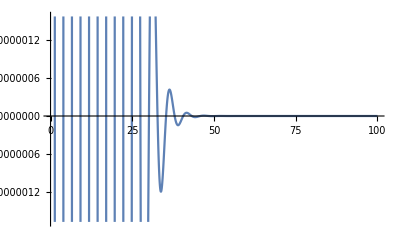

```mathematica
Plot[Re[Exp[-0.402437484 z]Exp[I 1.2 z]],{z,0,100}]
```

```mathematica
Exp[-0.402437484 z]Exp[I 1.2 z]/.{z->50}
```

-1.73783×10^-9-5.56175×10^-10 ⅈ

```mathematica
NIntegrate[G1sk[0.402437484,1.2]G1sk[0.402437484,-1.2]HeavisideTheta[Sqrt[x^2+y^2+z^2]-rc](Sqrt[x^2+y^2+z^2]-rc)^2,{x,-Infinity,+Infinity},{y,-Infinity,+Infinity},{z,-Infinity,+Infinity}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.3944375677457957064830727411644875969837239730741818713234225161×10^-1003 + 0.\ ⅈ and 5.686789223396264751799158752515074394024728165011006428205500413×10^-1003 for the integral and error estimates.

0.+0. ⅈ

```mathematica
NIntegrate[G1sk[0.402437484,1.2]G1sk[0.273904962,0.6]HeavisideTheta[Sqrt[x^2+y^2+z^2]-rc](Sqrt[x^2+y^2+z^2]-rc)^2,{x,-Infinity,+Infinity},{y,-Infinity,+Infinity},{z,-Infinity,+Infinity},WorkingPrecision->120]
```

NIntegrate::precw: The precision of the argument function (0.0971726\ ⅇ^(0.  + 1.8\ ⅈ)\ z - 0.676342\ (x^2 + y^2 + z^2)\ (-50 + √x^2 + y^2 + z^2)^2\ HeavisideTheta[-50 + √x^2 + y^2 + z^2]) is less than WorkingPrecision (120.).

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

NIntegrate[G1sk[0.402437,1.2] G1sk[0.273905,0.6] HeavisideTheta[√(x^2+y^2+z^2)-rc] (√(x^2+y^2+z^2)-rc)^2,{x,-∞,+∞},{y,-∞,+∞},{z,-∞,+∞},WorkingPrecision→120]

```mathematica
NIntegrate[G2pk[0.773904962,-0.3]G2pk[0.273904962,0.6]HeavisideTheta[Sqrt[x^2+y^2+z^2]-rc](Sqrt[x^2+y^2+z^2]-rc)^2,{x,-Infinity,+Infinity},{y,-Infinity,+Infinity},{z,-Infinity,+Infinity}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0126325  + 1.08471×10^-14\ ⅈ and 6.87704×10^-8 for the integral and error estimates.

0.0126325+1.08471×10^-14 ⅈ

```mathematica
NIntegrate[G2pk[0.773904962,-0.3]G2pk[0.273904962,0.6]HeavisideTheta[Sqrt[x^2+y^2+z^2]-rc](Sqrt[x^2+y^2+z^2]-rc)^2,{x,-Infinity,+Infinity},{y,-Infinity,+Infinity},{z,-Infinity,+Infinity}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0109623  + 3.59264×10^-14\ ⅈ and 1.89738×10^-7 for the integral and error estimates.

0.0109623+3.59264×10^-14 ⅈ

```mathematica
Integrate[G1sk[a,-kz]G1sk[a,kz],{x,-Infinity,+Infinity},{y,-Infinity,+Infinity},{z,-Infinity,+Infinity},Assumptions->{a>0,kz∈Reals}]
```

```mathematica
NIntegrate[G1sk[0.773904962,-0.3]G2pk[0.273904962,0.6]HeavisideTheta[Sqrt[x^2+y^2+z^2]-rc](Sqrt[x^2+y^2+z^2]-rc)^2,{x,-Infinity,+Infinity},{y,-Infinity,+Infinity},{z,-Infinity,+Infinity}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.27734×10^-17 + 0.00215395\ ⅈ and 8.30913×10^-8 for the integral and error estimates.

3.27734×10^-17+0.00215395 ⅈ

```mathematica
Integrate[x^n Exp[-a x^2],{x,1,Infinity}]
```

ConditionalExpression[1/2 ExpIntegralE[1/2-n/2,a],Re[n]>-1&&Re[a]>0]

```mathematica
Integrate[x Exp[-a x^2],{x,1,Infinity}]
```

ConditionalExpression[ⅇ^-a/(2 a),Re[a]>0]

```mathematica
NIntegrate[x^10 Exp[-20x^2],{x,1,Infinity}]
```

6.54249×10^-11

```mathematica
NIntegrate[x^0 Exp[-20 x^2],{x,1,Infinity}]
```

5.03269×10^-11

```mathematica
Gn[n_,a_]:=1/2 ExpIntegralE[1/2-n/2,a]
```

```mathematica
jlnsum[l_,n_,k_,p_]:=NSum[(-k^2/2)^m/((2m+2l+1)!!m!)Gn[n+l+2m,p],{m,0,5}]
```

```mathematica
jln[4,5,2,5]
```

0.000022133442657011509897554217037744

```mathematica
(2*1+1)!!
```

3

```mathematica
SetPrecision[jlnsum[1,2,2,5],15]
```

0.4

0 0.0002695178799634 0.0002695178799634 0.0008085536398903 1. 3.

1 -0.0001329621541153 0.0001365557258481 0.0009972161558646 -2. 15.

2 0.00002423094082719 0.0001607866666753 0.001272124393427 4. 105.

3 -2.386587957179×10^-6 0.0001584000787181 0.00169149421465 -8. 945.

4 1.516940140811×10^-7 0.0001585517727322 0.002365288914559 16. 10395.

5 -6.930632621461×10^-9 0.0001585448420996 0.003512141397379 -32. 135135.

6 2.451668564627×10^-10 0.0001585450872665 0.00559079265624 64. 2.027025×10^6

7 -7.089313365486×10^-12 0.0001585450801771 0.009619062949892 -128. 3.4459425×10^7

8 1.744388846417×10^-13 0.0001585450803516 0.01798810800971 256. 6.54729075×10^8

9 -3.760972102538×10^-15 0.0001585450803478 0.03665001071934 -512. 1.3749310575×10^10

10 7.255028244989×10^-17 0.0001585450803479 0.08130381828245 1024. 3.16234143225×10^11

11 -1.270704936748×10^-18 0.0001585450803479 0.1958029585778 -2048. 7.905853580625×10^12

12 2.042102203414×10^-20 0.0001585450803479 0.5097614870021 4096. 2.13458046676875×10^14

13 -3.03479330932×10^-22 0.0001585450803479 1.428005958306 -8192. 6.19028335362938×10^15

14 4.196226670101×10^-24 0.0001585450803479 4.284691669618 16384. 1.91898783962511×10^17

15 -5.425691000947×10^-26 0.0001585450803479 13.71168713748 -32768. 6.33265987076285×10^18

16 6.588434293794×10^-28 0.0001585450803479 46.62041006212 65536. 2.216430954767×10^20

17 -7.541640279452×10^-30 0.0001585450803479 167.8341500183 -131072. 8.20079453263789×10^21

18 8.164747390009×10^-32 0.0001585450803479 637.7704438644 262144. 3.19830986772878×10^23

19 -8.384851909106×10^-34 0.0001585450803479 2551.082449252 -524288. 1.3113070457688×10^25

20 8.189855868107×10^-36 0.0001585450803479 10714.54696065 1.048576×10^6 5.63862029680584×10^26

```mathematica
Gn[1,5]//N
```

0.000673795

```mathematica
jlnsum[l_,n_,k_,p_]:=Module[{val,term,m},
val=0;
Print[SetPrecision[k^2/(2p),15]];
For[m=0,m≤20,m++,
term=(-k^2/2)^m/((2m+2l+1)!!m!)Gn[n+l+2m,p];
val+=term;
Print[m," ",SetPrecision[term,15]," ",SetPrecision[val,15]," ",SetPrecision[Gn[n+l+2m,p],15]," ",SetPrecision[(-k^2/2)^m,15]," ",SetPrecision[(2m+2l+1)!!,15]];
];
]
```

```mathematica
x0=63/10;
y0=44/10;
```

```mathematica
xxx=2/10+8/10*I;
```

```mathematica
xx=Re[xxx]/x0;
yy=Im[xxx]/y0;
```

```mathematica
QQ=xx*xx+yy*yy;
```

```mathematica
Sqrt[QQ]//N
```

0.184569

```mathematica
QQ2=(1-85/100*yy)Sqrt[QQ]//N
```

0.156045

```mathematica
nsum=16+132*QQ2//N
```

36.5979

```mathematica
SetPrecision[Faddeeva[xxx]-Exp[-xxx^2](1+2I/Sqrt[Pi]Sum[xxx^(2n+1)/(2n+1)/n!,{n,0,nsum}]),32]
```

0.+0. ⅈ

```mathematica
Re[SetPrecision[Faddeeva[6+3I],36]]
```

0.0385545974485933588129365377897848

```mathematica
0.0385545974485933588129365395234208e-02
```

```mathematica
Im[SetPrecision[Faddeeva[6+3I],36]]
```

0.07536948707088668074064659643796917

```mathematica
0.0753694870708866807406465964392224e-02
```

```mathematica
(*nsum=20;*)
```

```mathematica
SetPrecision[Exp[-xxx^2](1+2I/Sqrt[Pi]Sum[xxx^(2n+1)/(2n+1)/n!,{n,0,nsum}]),32]
```

0.26235030647440549897749950425+0.03421694920731051151507966712 ⅈ